For Simple Convex Problems, this works

```mathematica
S[x_] := {x[[1]]^2,x[[2]]^2,x[[3]]^2};
maxIter = 25;
InitGuess = {10,10,10};
Table[If[i >= 0,
Subscript[J, i] = Subscript[J, i-1] + 1 / (Norm[Subscript[x, i] - Subscript[x, i-1]]^2)* KroneckerProduct[(S[Subscript[x, i]] - S[Subscript[x, i-1]] - Subscript[J, i-1].(Subscript[x, i] - Subscript[x, i-1])),(Subscript[x, i] - Subscript[x, i-1])];
Subscript[x, i+1] = Subscript[x, i] - Inverse[Subscript[J, i]].S[Subscript[x, i]],
Subscript[x, -1] = InitGuess;Subscript[x, 0] = InitGuess + {0.01,0.01,0.01}; 
Subscript[J, -1] = IdentityMatrix[3];
],{i,-1,maxIter-1}];
Subscript[J, maxIter-1]
Subscript[x, maxIter]
```

{{0.666739,-0.333261,-0.333261},{-0.333261,0.666739,-0.333261},{-0.333261,-0.333261,0.666739}}

{0.0000509433,0.0000509433,0.0000509433}

Try Shooting Method for Fixed Time Problem:

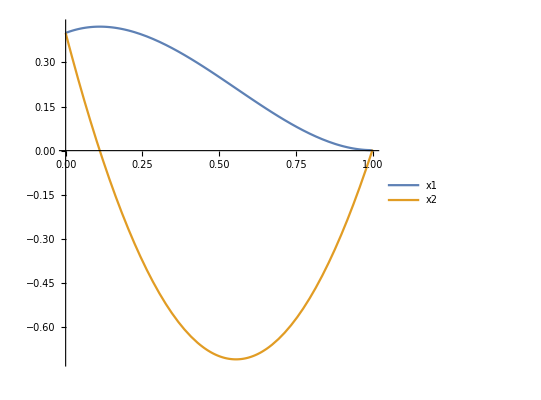
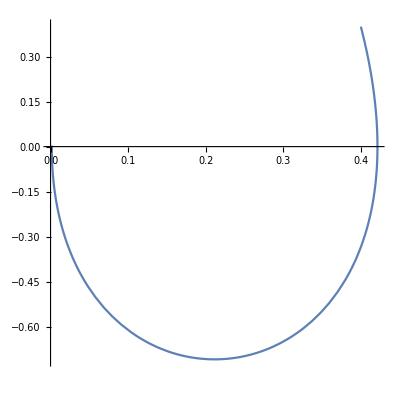
-Graphics- | -Graphics-

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
ϕh[x0_,p0_,T_,h_] := Module[{x,xStar,f,n,xFinal,output},
f[x_] := {x[[2]],-x[[4]],0,-x[[3]]};
If[T < 0, output = Join[x0,p0],
n = IntegerPart[T/h];
xFinal = Table[If[i != -1,Subscript[xStar, i+1] = Subscript[xStar, i] +h*f[Subscript[xStar, i]],Subscript[xStar, 0] = {x0[[1]],x0[[2]],p0[[1]],p0[[2]]}],{i,-1,n-1}];
output = xFinal[[n+1]];
];
output
]
ICs = {0.4,0.4};maxIter = 5;h = 0.001;T = 1;
InitGuess = {0,0};
S[x_]:= Table[ϕh[ICs,x,T,h][[i]],{i,1,2}];
Table[If[i >= 0,
Subscript[J, i] = Subscript[J, i-1] + 1 / (Norm[Subscript[x, i] - Subscript[x, i-1]]^2)* KroneckerProduct[(S[Subscript[x, i]] - S[Subscript[x, i-1]] - Subscript[J, i-1].(Subscript[x, i] - Subscript[x, i-1])),(Subscript[x, i] - Subscript[x, i-1])];
Subscript[x, i+1] = Subscript[x, i] - Inverse[Subscript[J, i]].S[Subscript[x, i]],
Subscript[x, -1] = InitGuess;Subscript[x, 0] = InitGuess + {0.01,0.01}; 
Subscript[J, -1] = IdentityMatrix[2];
],{i,-1,maxIter-1}];
eq={x1'[t]==x2[t],x2'[t]== -λ2[t],λ1'[t] == 0,λ2'[t] == -λ1[t]};
init={x1[0]==ICs[[1]],x2[0]==ICs[[2]],λ1[0]==Subscript[x, maxIter][[1]],λ2[0]==Subscript[x, maxIter][[2]]};
{x1s,x2s,λ1s,λ2s}=NDSolveValue[{eq,init},{x1,x2,λ1,λ2},{t,0,T},Method->{"DiscontinuityProcessing"->None}];

p1 = Plot[{x1s[t],x2s[t]},{t,0,T},PlotLegends->{"x1","x2"},AspectRatio->1,ImageSize->400];
p2 = ParametricPlot[{x1s[t],x2s[t]},{t,0,T},AspectRatio->1,ImageSize->400];
Grid[{{p1,p2}}]
```

Discrete Flow Function and Shooting Function

{{3.00039,-2.80258,0.458962},{1.14239,-1.06246,0.965545},{0.0813726,-0.741236,-0.157219}}

{1.42694,1.54487,1.78485}

{0.0059,-1.35308×10^-16,0.00491567}

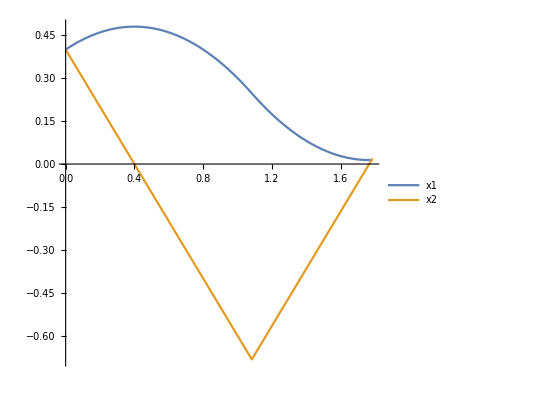
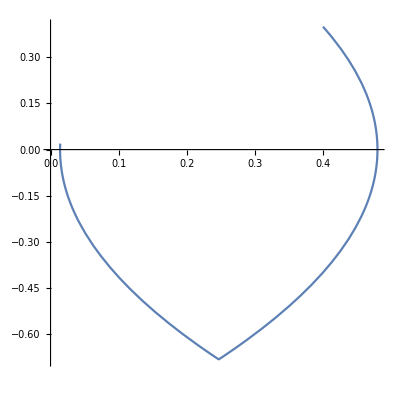
-Graphics- | -Graphics-

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
ϕh[x0_,p0_,T_,h_] := Module[{x,xStar,f,n,xFinal,output},
f[x_] := {x[[2]],-Sign[x[[4]]],0,-x[[3]]};
n = Abs[IntegerPart[T/h]];
If[T < 0, 
xFinal = Table[If[i != -1,Subscript[xStar, i+1] = Subscript[xStar, i] -h*f[Subscript[xStar, i]],Subscript[xStar, 0] = {x0[[1]],x0[[2]],p0[[1]],p0[[2]]}],{i,-1,n-1}];
output = xFinal[[n+1]],
xFinal = Table[If[i != -1,Subscript[xStar, i+1] = Subscript[xStar, i] +h*f[Subscript[xStar, i]],Subscript[xStar, 0] = {x0[[1]],x0[[2]],p0[[1]],p0[[2]]}],{i,-1,n-1}];
output = xFinal[[n+1]];
];
output
]
H[x_] := 1 + x[[3]]*x[[2]] + x[[4]]*(-Sign[x[[4]]]);
ICs = {0.4,0.4};maxIter = 13;h = 0.01;
InitGuess = {1,1,2};
S[x_]:= Module[{p0,T},
p0 = Table[x[[i]],{i,1,2}];
T = x[[3]];
Flatten[{Table[ϕh[ICs,p0,T,h][[i]],{i,1,2}],H[ϕh[ICs,p0,T,h]]},1]
]
Table[If[i >= 0,
Subscript[J, i] = Subscript[J, i-1] + 1 / (Norm[Subscript[x, i] - Subscript[x, i-1]]^2)* KroneckerProduct[(S[Subscript[x, i]] - S[Subscript[x, i-1]] - Subscript[J, i-1].(Subscript[x, i] - Subscript[x, i-1])),(Subscript[x, i] - Subscript[x, i-1])];
Subscript[x, i+1] = Subscript[x, i] - Inverse[Subscript[J, i]].S[Subscript[x, i]],
Subscript[x, -1] = InitGuess;Subscript[x, 0] = InitGuess + {0.01,0.01,0.2}; 
Subscript[J, -1] = IdentityMatrix[3];
],{i,-1,maxIter-1}];
Subscript[J, maxIter-1]
Subscript[x, maxIter]
S[Subscript[x, maxIter]]

eq={x1'[t]==x2[t],x2'[t]== -Sign[λ2[t]],λ1'[t] == 0,λ2'[t] == -λ1[t]};
init={x1[0]==ICs[[1]],x2[0]==ICs[[2]],λ1[0]==Subscript[x, maxIter][[1]],λ2[0]==Subscript[x, maxIter][[2]]};
{x1s,x2s,λ1s,λ2s}=NDSolveValue[{eq,init},{x1,x2,λ1,λ2},{t,0,Subscript[x, maxIter][[3]]},Method->{"DiscontinuityProcessing"->None}];
p1 = Plot[{x1s[t],x2s[t]},{t,0,Subscript[x, maxIter][[3]]},PlotLegends->{"x1","x2"},AspectRatio->1,ImageSize->400];
p2 = ParametricPlot[{x1s[t],x2s[t]},{t,0,Subscript[x, maxIter][[3]]},AspectRatio->1,ImageSize->400];
Grid[{{p1,p2}}]
```

Thus this approach works. However the initial guesses (both of them) are very crucial for convergence. Try for other Initial Conditions

{{0.110027,-1.84542,-1.96922},{-0.962113,-2.80451,-5.82367},{1.39717,2.20203,4.19892}}

{-1.43579,-0.411018,0.987507}

{-0.0019,-1.97758×10^-16,0.00394742}

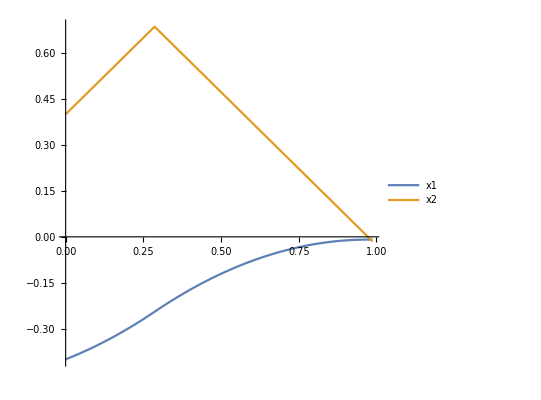
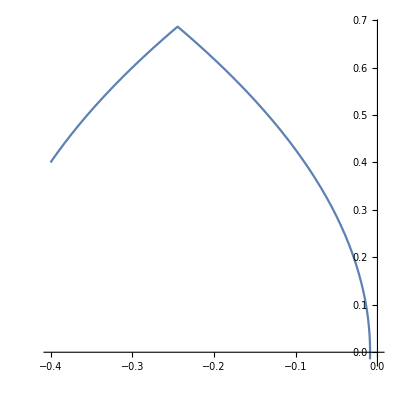
-Graphics- | -Graphics-

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
ϕh[x0_,p0_,T_,h_] := Module[{x,xStar,f,n,xFinal,output},
f[x_] := {x[[2]],-Sign[x[[4]]],0,-x[[3]]};
n = Abs[IntegerPart[T/h]];
If[T < 0, 
xFinal = Table[If[i != -1,Subscript[xStar, i+1] = Subscript[xStar, i] -h*f[Subscript[xStar, i]],Subscript[xStar, 0] = {x0[[1]],x0[[2]],p0[[1]],p0[[2]]}],{i,-1,n-1}];
output = xFinal[[n+1]],
xFinal = Table[If[i != -1,Subscript[xStar, i+1] = Subscript[xStar, i] +h*f[Subscript[xStar, i]],Subscript[xStar, 0] = {x0[[1]],x0[[2]],p0[[1]],p0[[2]]}],{i,-1,n-1}];
output = xFinal[[n+1]];
];
output
]
H[x_] := 1 + x[[3]]*x[[2]] + x[[4]]*(-Sign[x[[4]]]);
ICs = {-0.4,0.4};maxIter = 55;h = 0.01;
InitGuess = {0,0,2};
S[x_]:= Module[{p0,T},
p0 = Table[x[[i]],{i,1,2}];
T = x[[3]];
Flatten[{Table[ϕh[ICs,p0,T,h][[i]],{i,1,2}],H[ϕh[ICs,p0,T,h]]},1]
]
Table[If[i >= 0,
Subscript[J, i] = Subscript[J, i-1] + 1 / (Norm[Subscript[x, i] - Subscript[x, i-1]]^2)* KroneckerProduct[(S[Subscript[x, i]] - S[Subscript[x, i-1]] - Subscript[J, i-1].(Subscript[x, i] - Subscript[x, i-1])),(Subscript[x, i] - Subscript[x, i-1])];
Subscript[x, i+1] = Subscript[x, i] - Inverse[Subscript[J, i]].S[Subscript[x, i]],
Subscript[x, -1] = InitGuess;Subscript[x, 0] = InitGuess + {0.01,0.01,0.2}; 
Subscript[J, -1] = IdentityMatrix[3];
],{i,-1,maxIter-1}];
Subscript[J, maxIter-1]
Subscript[x, maxIter]
S[Subscript[x, maxIter]]
eq={x1'[t]==x2[t],x2'[t]== -Sign[λ2[t]],λ1'[t] == 0,λ2'[t] == -λ1[t]};
init={x1[0]==ICs[[1]],x2[0]==ICs[[2]],λ1[0]==Subscript[x, maxIter][[1]],λ2[0]==Subscript[x, maxIter][[2]]};
{x1s,x2s,λ1s,λ2s}=NDSolveValue[{eq,init},{x1,x2,λ1,λ2},{t,0,Subscript[x, maxIter][[3]]},Method->{"DiscontinuityProcessing"->None}];
p1 = Plot[{x1s[t],x2s[t]},{t,0,Subscript[x, maxIter][[3]]},PlotLegends->{"x1","x2"},AspectRatio->1,ImageSize->400];
p2 = ParametricPlot[{x1s[t],x2s[t]},{t,0,Subscript[x, maxIter][[3]]},AspectRatio->1,ImageSize->400];
Grid[{{p1,p2}}]
```

{{-59.0918,-58.5024,-25.779},{-45.9395,-43.1773,-37.1985},{47.9471,42.3059,19.692}}

{-0.872974,-0.113925,1.28034}

{0.0046,-7.5287×10^-16,-0.00348223}

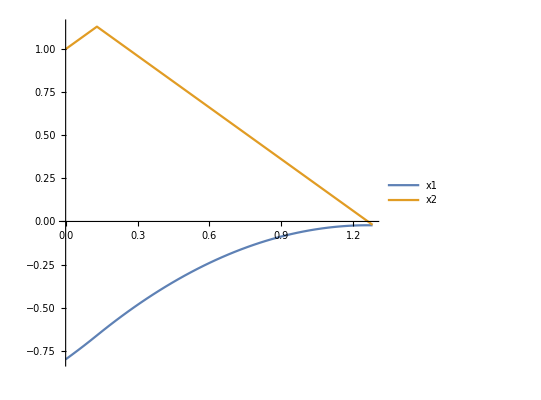
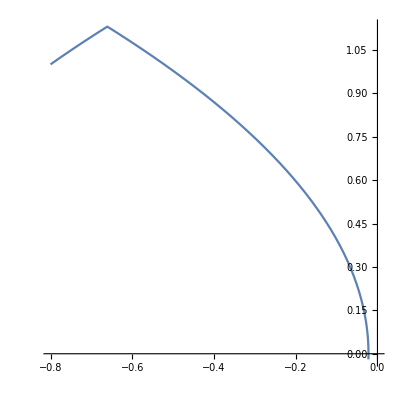
-Graphics- | -Graphics-

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
ϕh[x0_,p0_,T_,h_] := Module[{x,xStar,f,n,xFinal,output},
f[x_] := {x[[2]],-Sign[x[[4]]],0,-x[[3]]};
n = Abs[IntegerPart[T/h]];
If[T < 0, 
xFinal = Table[If[i != -1,Subscript[xStar, i+1] = Subscript[xStar, i] -h*f[Subscript[xStar, i]],Subscript[xStar, 0] = {x0[[1]],x0[[2]],p0[[1]],p0[[2]]}],{i,-1,n-1}];
output = xFinal[[n+1]],
xFinal = Table[If[i != -1,Subscript[xStar, i+1] = Subscript[xStar, i] +h*f[Subscript[xStar, i]],Subscript[xStar, 0] = {x0[[1]],x0[[2]],p0[[1]],p0[[2]]}],{i,-1,n-1}];
output = xFinal[[n+1]];
];
output
]
H[x_] := 1 + x[[3]]*x[[2]] + x[[4]]*(-Sign[x[[4]]]);
ICs = {-0.8,1};maxIter = 63;h = 0.01;
InitGuess = {0,0,2};
S[x_]:= Module[{p0,T},
p0 = Table[x[[i]],{i,1,2}];
T = x[[3]];
Flatten[{Table[ϕh[ICs,p0,T,h][[i]],{i,1,2}],H[ϕh[ICs,p0,T,h]]},1]
]
Table[If[i >= 0,
Subscript[J, i] = Subscript[J, i-1] + 1 / (Norm[Subscript[x, i] - Subscript[x, i-1]]^2)* KroneckerProduct[(S[Subscript[x, i]] - S[Subscript[x, i-1]] - Subscript[J, i-1].(Subscript[x, i] - Subscript[x, i-1])),(Subscript[x, i] - Subscript[x, i-1])];
Subscript[x, i+1] = Subscript[x, i] - Inverse[Subscript[J, i]].S[Subscript[x, i]],
Subscript[x, -1] = InitGuess;Subscript[x, 0] = InitGuess + {0.01,0.01,0.2}; 
Subscript[J, -1] = IdentityMatrix[3];
],{i,-1,maxIter-1}];
Subscript[J, maxIter-1]
Subscript[x, maxIter]
S[Subscript[x, maxIter]]
eq={x1'[t]==x2[t],x2'[t]== -Sign[λ2[t]],λ1'[t] == 0,λ2'[t] == -λ1[t]};
init={x1[0]==ICs[[1]],x2[0]==ICs[[2]],λ1[0]==Subscript[x, maxIter][[1]],λ2[0]==Subscript[x, maxIter][[2]]};
{x1s,x2s,λ1s,λ2s}=NDSolveValue[{eq,init},{x1,x2,λ1,λ2},{t,0,Subscript[x, maxIter][[3]]},Method->{"DiscontinuityProcessing"->None}];
p1 = Plot[{x1s[t],x2s[t]},{t,0,Subscript[x, maxIter][[3]]},PlotLegends->{"x1","x2"},AspectRatio->1,ImageSize->400];
p2 = ParametricPlot[{x1s[t],x2s[t]},{t,0,Subscript[x, maxIter][[3]]},AspectRatio->1,ImageSize->400];
Grid[{{p1,p2}}]
```